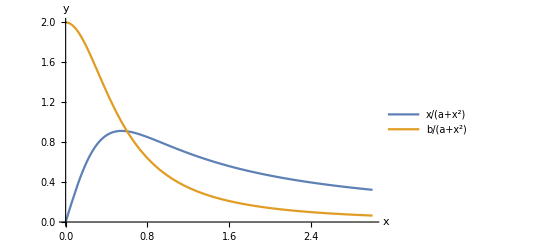

```mathematica
p1=Plot[{x/(0.3+x^2),0.6/(0.3+x^2)},{x,0,3},PlotRange->All,AxesLabel->{x,y},PlotLegends->{x/(a+x^2),b/(a+x^2)}]
```

```mathematica
Export["nullglyco.jpg",p1,CompressionLevel->0]
```

nullglyco.jpg

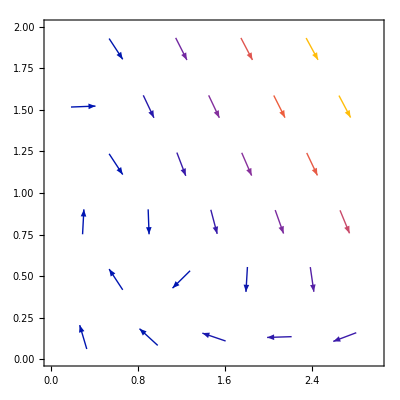

```mathematica
vp1=VectorPlot[{-x+0.3*y+y*x^2,0.6-0.3*y-y*x^2},{x,0,3},{y,0,2},VectorPoints->5]
```

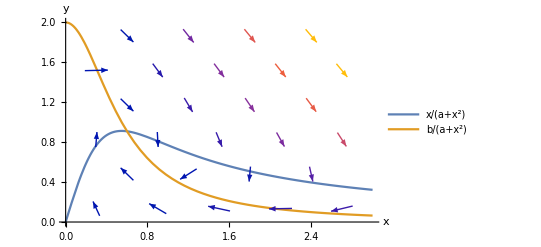

```mathematica
gf=Show[p1,vp1]
```

```mathematica
Export["glycofield.jpg",gf,CompressionLevel->0]
```

glycofield.jpg

```mathematica
N[Solve[-x+13/5==x/(3/10+x^2),x]]
```

{{x→2.16608},{x→0.216959-0.559487 ⅈ},{x→0.216959+0.559487 ⅈ}}

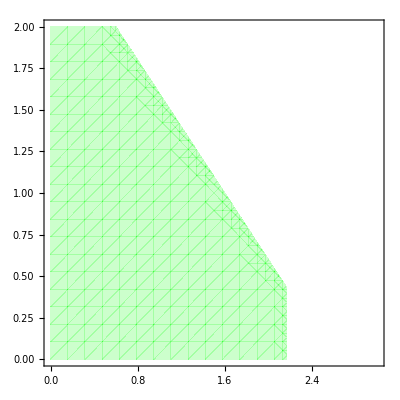

```mathematica
rp1=RegionPlot[(x>0)&&(y>0)&&(y<2)&&(y<-x+13/5)&&(x<2.1660815470479315),{x,0,3},{y,0,2},PlotStyle->Directive[Green,Opacity[0.2]],BoundaryStyle->None]
```

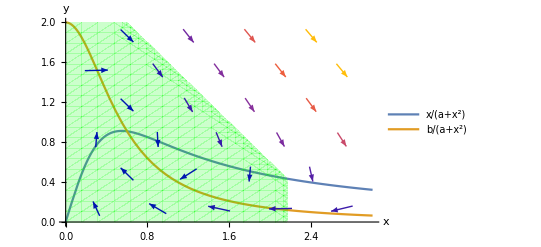

```mathematica
r1=Show[p1,rp1,vp1]
```

```mathematica
Export["glycooregion.jpg",r1,CompressionLevel->0]
```

glycooregion.jpg

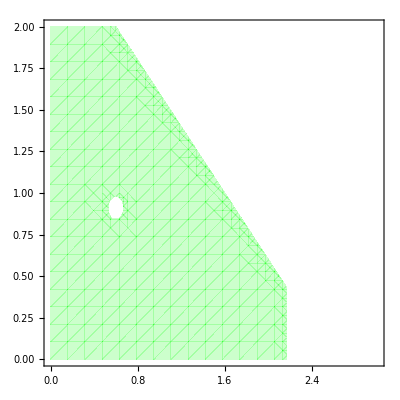

```mathematica
rp2=RegionPlot[(x>0)&&(y>0)&&(y<2)&&(y<-x+13/5)&&(x<2.1660815470479315)&&((x-0.6)^2+(y-0.6/(0.3+0.6^2))^2>0.005),{x,0,3},{y,0,2},PlotStyle->Directive[Green,Opacity[0.2]],BoundaryStyle->None]
```

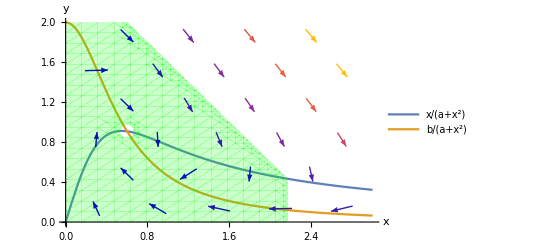

```mathematica
r2=Show[p1,rp2,vp1]
```

```mathematica
Export["glycotregion.jpg",r2,CompressionLevel->0]
```

glycotregion.jpg

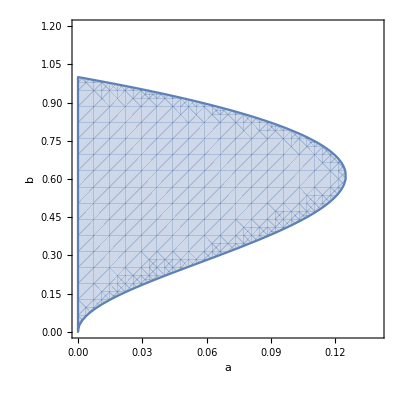

```mathematica
rp3=RegionPlot[a>0&&b>0&&b^2<(1-2*a+Sqrt[1-8*a])/2&&b^2>(1-2*a-Sqrt[1-8*a])/2,{a,0,0.14},{b,0,1.2},FrameLabel->{a,b}]
```

```mathematica
Export["glycopspace.jpg",rp3,CompressionLevel->0]
```

glycopspace.jpg

```mathematica
sol=NDSolve[{x'[t]==-x[t]+0.06*y[t]+y[t]*x[t]^2,y'[t]==0.6-0.06*y[t]-y[t]*x[t]^2,x[0]==0.001,y[0]==0.001},{x,y},{t,0,30}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

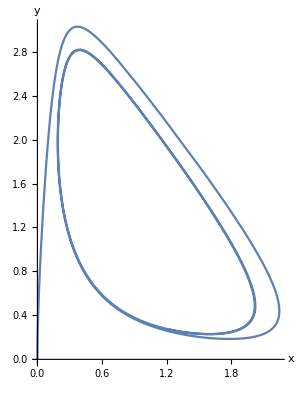

```mathematica
spp=ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,30},AxesLabel->{x,y}]
```

```mathematica
Export["glycoctraj.jpg",spp,CompressionLevel->0]
```

glycoctraj.jpg

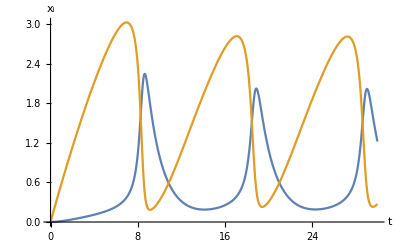

```mathematica
sp=Plot[Evaluate[{x[t],y[t]}/.sol],{t,0,30},AxesLabel->{t,Subscript[x,i]}]
```

```mathematica
Export["glycocsols.jpg",sp,CompressionLevel->0]
```

glycocsols.jpg